Modify these as necessary.

```mathematica
importPath="/Users/jackshi/Desktop/policy_rollout_data/WheeledLeft.csv";
exportPath="/Users/jackshi/Desktop/policy_rollout.mov";
tf=200;
L=2;
xmin=-12;
xmax=6;
ymin=-16;
ymax=6;
```

```mathematica
numFrames = 1000;
terrarium = {{xmin, xmax}, {ymin, ymax}, {-L/2, L/2}};
```

Import and set up data.

```mathematica
data=Transpose[Import[importPath]];
x0=ListInterpolation[data[[1]],{{0,tf}}];
y0=ListInterpolation[data[[2]],{{0,tf}}];
th0=ListInterpolation[data[[3]],{{0,tf}}];
a1=ListInterpolation[data[[4]],{{0,tf}}];
a2=ListInterpolation[data[[5]],{{0,tf}}];
```

```mathematica
th1=th0[#]+a1[#]&;
th2=th1[#]+a2[#]&;
x1=x0[#]+L/2 Cos[th0[#]]+L/2 Cos[th1[#]]&;
y1=y0[#]+L/2 Sin[th0[#]]+L/2 Sin[th1[#]]&;
x2=x1[#]+L/2 Cos[th1[#]]+L/2 Cos[th2[#]]&;
y2=y1[#]+L/2 Sin[th1[#]]+L/2 Sin[th2[#]]&;
```

Check the plots to make sure.

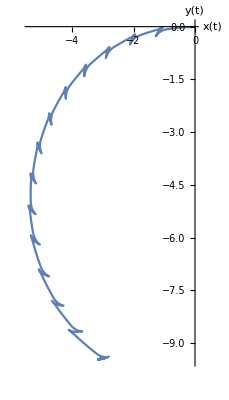

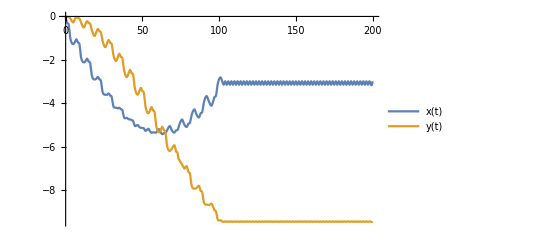

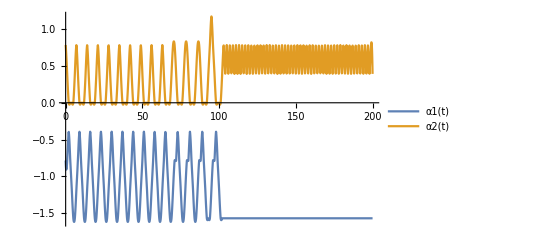

```mathematica
ParametricPlot[{x0[k],y0[k]},{k,0,tf},AxesLabel->{x[t],y[t]}]
Plot[{x0[k],y0[k]},{k,0,tf},PlotLegends->{x[t],y[t]}]
Plot[{a1[t],a2[t]},{t,0,tf},PlotLegends->{α1[t],α2[t]}]
```

Here are some purely aesthetic parameters.

```mathematica
wheelRadius = 1/8 L;
linkThickness = 1/12 L;
wheelThickness = 2/3 linkThickness;
hingeRadius = 2/3 linkThickness;
hingeHeight = 3/2 linkThickness;
```

Here are the elements of a 3 D cartoon.

```mathematica
wheel[xCenter_, yCenter_, θ_] = {RGBColor[.6,0,0], Opacity[1.0], EdgeForm[Black],Cylinder[{{xCenter - 1/2 wheelThickness Sin[θ], yCenter + 1/2 wheelThickness Cos[θ], wheelRadius}, {xCenter + 1/2 wheelThickness Sin[θ], yCenter - 1/2 wheelThickness Cos[θ], wheelRadius}}, wheelRadius]};
link[xCenter_, yCenter_, θ_] = {RGBColor[.2,.6,.8], Opacity[1.0], EdgeForm[Black],Rotate[Cuboid[{xCenter - L/2, yCenter - 1/2 linkThickness, wheelRadius - 1/2 linkThickness}, {xCenter + L/2, yCenter + 1/2 linkThickness, wheelRadius + 1/2 linkThickness}], θ, {0, 0, 1}, {xCenter, yCenter, 0}]};
hinge[xCenter_, yCenter_] = {RGBColor[.6,.6,.2], Opacity[1.0], EdgeForm[Black],Cylinder[ {{xCenter, yCenter, wheelRadius - 1/2 hingeHeight}, {xCenter, yCenter, wheelRadius + 1/2 hingeHeight}}, hingeRadius]};
completeSnake[{x1_, y1_}, θ1_, {x2_, y2_}, θ2_, {x3_, y3_}, θ3_] = {link[x1, y1, θ1], wheel[x1, y1, θ1], hinge[x1 + L/2 Cos[θ1], y1 + L/2 Sin[θ1]], link[x2, y2, θ2], wheel[x2, y2, θ2], hinge[x2 + L/2 Cos[θ2], y2 + L/2 Sin[θ2]],link[x3, y3, θ3], wheel[x3, y3, θ3]};
Show[Graphics3D[{link[x1[k],y1[k],th1[k]],link[x2[k],y2[k],th2[k]],link[x0[k],y0[k],th0[k]],wheel[x1[k],y1[k],th1[k]],wheel[x2[k],y2[k],th2[k]],wheel[x0[k],y0[k],th0[k]]}]/.k->3.2,Boxed->False]
```

-Graphics3D-

Animate!

```mathematica
cartoon=Graphics3D[{link[x1[k],y1[k],th1[k]],link[x2[k],y2[k],th2[k]],link[x0[k],y0[k],th0[k]],wheel[x1[k],y1[k],th1[k]],wheel[x2[k],y2[k],th2[k]],wheel[x0[k],y0[k],th0[k]]},PlotRange -> terrarium,ImageSize -> Large];
threeDframes=Table[Show[cartoon], {k, 0, tf, tf/numFrames}];
ListAnimate[threeDframes]
```

```mathematica
Export[exportPath,threeDframes,ImageResolution->800,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"];
```